# Ferromagnetic Hysteresis with Stress

## Front matter

### Setup the notebook

Reset the environment

```mathematica
Remove["Global`*"]
```

#### Load the initialize cells from Github

```mathematica
Get[NotebookDirectory[]<>"InitWorksheet.wl"];
```

#### Unit definition

```mathematica
$UnitSystem="Metric"
```

Metric

#### Commonly used substitutions

```mathematica
subFmtPub= {μo->Subscript[μ, o],μr->Subscript[μ, r],μri->Subscript[μ, r,i],μrd->Subscript[μ, r,d],μrxi->Subscript[μ, rx,i],
Ar->A,do->Subscript[d, o],
ℛspi->Subscript[ℛ, sp,i],ℛsprecti->Subscript[ℛ, sprect,i],ℛspcirci->Subscript[ℛ, spcirc,i],ℛopengapi->Subscript[ℛ, opengap,i],
𝒫spi->Subscript[𝒫, sp,i],𝒫sprecti->Subscript[𝒫, sprect,i],𝒫spcirci->Subscript[𝒫, spcirc,i],𝒫opengapi->Subscript[𝒫, br],
𝒫br->Subscript[𝒫, br],𝒫d->Subscript[𝒫, d],𝒫s->Subscript[𝒫, s],𝒫t->Subscript[𝒫, t],𝒫tall ->Subscript[𝒫, t,all],
𝒫0d->Subscript[𝒫, 0,d],𝒫0s->Subscript[𝒫, 0,s],
𝒫1d->Subscript[𝒫, 1,d],𝒫1s->Subscript[𝒫, 1,s],
𝒫2d->Subscript[𝒫, 2,d],𝒫2s->Subscript[𝒫, 2,s],
𝒫1->Subscript[𝒫, 1],𝒫2->Subscript[𝒫, 2],𝒫sd->Subscript[𝒫, s,d],𝒫3->Subscript[𝒫, 3],
ℛcore->Subscript[ℛ, core],ℛsd->Subscript[ℛ, sd], ℛ2->Subscript[ℛ, 2],
ℛgaps->Subscript[ℛ, gap,s], ℛt->Subscript[ℛ, t],ℛ3->Subscript[ℛ, 3],ℛgapd->Subscript[ℛ, gap,d],
𝒫core->Subscript[𝒫, core],
gu->Subscript[g, u],
Vs->Subscript[V, s],Id->Subscript[Ii, d],
vout->Subscript[v, output], v3->Subscript[v, 3],v4->Subscript[v, 4], v1->Subscript[v, 1], v2->Subscript[v, 2],
id->Subscript[i, d],z1->Subscript[z, 1],z2->Subscript[z, 2],z3->Subscript[z, 3],z4->Subscript[z, 4],
𝒫gapd->Subscript[𝒫, gap,d],𝒫gaps->Subscript[𝒫, gap,s],
𝒫breddy->Subscript[𝒫, br,eddy],𝒫deddy->Subscript[𝒫, d,eddy],𝒫seddy->Subscript[𝒫, s,eddy],
λs->Subscript[λ, s],c11->Subscript[c, 11],c12->Subscript[c, 12],
Heff->Subscript[H, eff],σ0->Subscript[σ, 0],Hσ->Subscript[H, σ],
γ1->Subscript[γ, 1],γ2->Subscript[γ, 2],
Man->Subscript[M, an],DMan->Subscript[DM, an],kb->Subscript[k, b]}
```

{μo→μ_o,μr→μ_r,μri→μ_(r,i),μrd→μ_(r,d),μrxi→μ_(rx,i),Ar→A,do→d_o,ℛspi→ℛ_(sp,i),ℛsprecti→ℛ_(sprect,i),ℛspcirci→ℛ_(spcirc,i),ℛopengapi→ℛ_(opengap,i),𝒫spi→𝒫_(sp,i),𝒫sprecti→𝒫_(sprect,i),𝒫spcirci→𝒫_(spcirc,i),𝒫opengapi→𝒫_br,𝒫br→𝒫_br,𝒫d→𝒫_d,𝒫s→𝒫_s,𝒫t→𝒫_t,𝒫tall→𝒫_(t,all),𝒫0d→𝒫_(0,d),𝒫0s→𝒫_(0,s),𝒫1d→𝒫_(1,d),𝒫1s→𝒫_(1,s),𝒫2d→𝒫_(2,d),𝒫2s→𝒫_(2,s),𝒫1→𝒫_1,𝒫2→𝒫_2,𝒫sd→𝒫_(s,d),𝒫3→𝒫_3,ℛcore→ℛ_core,ℛsd→ℛ_sd,ℛ2→ℛ_2,ℛgaps→ℛ_(gap,s),ℛt→ℛ_t,ℛ3→ℛ_3,ℛgapd→ℛ_(gap,d),𝒫core→𝒫_core,gu→g_u,Vs→V_s,Id→Ii_d,vout→v_output,v3→v_3,v4→v_4,v1→v_1,v2→v_2,id→i_d,z1→z_1,z2→z_2,z3→z_3,z4→z_4,𝒫gapd→𝒫_(gap,d),𝒫gaps→𝒫_(gap,s),𝒫breddy→𝒫_(br,eddy),𝒫deddy→𝒫_(d,eddy),𝒫seddy→𝒫_(s,eddy),λs→λ_s,c11→c_11,c12→c_12,Heff→H_eff,σ0→σ_0,Hσ→H_σ,γ1→γ_1,γ2→γ_2,Man→M_an,DMan→DM_an,kb→k_b}

```mathematica
subCode={μo->muo,μr->mur,μri->muri,μrd->murd,μrxi->murxi,
𝒫br->Pbr,𝒫d->Pd,𝒫s->Ps,𝒫t->Pt,𝒫3->P3,
ρ->rho, ω->omega,δ->delta,
𝒫0s->P0s,𝒫1s->P1s,𝒫2s->P2s,𝒫sd->Psd,𝒫eq->Peq,𝒫core->Pcore,𝒫->P,
𝒫breddy->Pbreddy,𝒫deddy->Pdeddy,𝒫seddy->Pseddy}
```

{μo→muo,μr→mur,μri→muri,μrd→murd,μrxi→murxi,𝒫br→Pbr,𝒫d→Pd,𝒫s→Ps,𝒫t→Pt,𝒫3→P3,ρ→rho,ω→omega,δ→delta,𝒫0s→P0s,𝒫1s→P1s,𝒫2s→P2s,𝒫sd→Psd,𝒫eq→Peq,𝒫core→Pcore,𝒫→P,𝒫breddy→Pbreddy,𝒫deddy→Pdeddy,𝒫seddy→Pseddy}

#### Assumptions and nomenclature

Assumptions about which parameters are reals:

```mathematica
$Assumptions={R1∈Reals,R2∈Reals,R3∈Reals, ℙ∈Reals,  ℙ12∈Reals, ℙ3∈Reals, ω ∈Reals, ϵ ∈Reals}
```

{R1∈ℝ,R2∈ℝ,R3∈ℝ,ℙ∈ℝ,ℙ12∈ℝ,ℙ3∈ℝ,ω∈ℝ,ϵ∈ℝ}

LaPlace nomenclature

```mathematica
LaplaceSub = {vs-> Vs,vd-> Vd,vsc-> Vsc,
i1-> I1,i2-> I2,i3-> I3,
is->Is, id->Id, it->It}
```

{vs→Vs,vd→Vd,vsc→Vsc,i1→I1,i2→I2,i3→I3,is→Is,id→Id,it→It}

## Problem setup

### Reference:

[1] 	D. Jiles and D. Atherton, “Ferromagnetic hysteresis,” in IEEE Transactions on Magnetics, vol. 19, no. 5, pp. 2183-2185, September 1983, doi: 10.1109/TMAG.1983.1062594.
[2]  	Jiles, D. C., and D. L. Atherton. “Theory of Ferromagnetic Hysteresis.” Journal of Magnetism and Magnetic Materials, vol. 61, nos. 1–2, 1986, pp. 48–60.
[3]  	Jiles, D. C. “Theory of the Magnetomechanical Effect.” Journal of Physics D: Applied Physics, vol. 28, 1995, pp. 1537–1546.

### Diagrams and drawings

-Graphics-

-Graphics-

### Nomenclature:

a 		Anhysteretic magnetization shape parameter, A/m
k 		Anhysteretic factor describing pinning energy, A/m
H 		Internal magnetic field, A/m
H_σ 		Internal magnetic field due to stress, A/m
M 		Bulk magnetization, A/m
M_s		Saturation magnetization,  A/m
α 		mean field parameter, -
θ 		Angle between stress and magnetic field, radians
μ_o 		Permeability of a vacuum, H/m
ν 		Poisson’s ratio, -
σ 		Stress, Pa
σ_0 		Applied stress, Pa

### Common equations

#### Effective internal magnetic field

Begin with the fundamental equation for the effective field, Eq (3) in [1]:

```mathematica
eqnEffField = Heff==H + α M +Hσ;
eqnEffField/.subFmtPub
```

H_eff==H+M α+H_σ

#### Internal magnetic field due to stress

Jiles makes a good point about how the magnetic field may be co-axial to the applied stress, Eq (4):

```mathematica
eqnStressMagField = σ == σ0*(Cos[θ]^2-ν Sin[θ]^2);
HoldForm[Evaluate[eqnStressMagField]]/.subFmtPub
```

σ==σ_0 (Cos[θ]^2-ν Sin[θ]^2)

From Eq. (5) in [3] Jiles defines the internal field due to stress:

```mathematica
eqnMagFieldDueToStress = Hσ==(3/2)*(σ/μo)* dλdMσ;
eqnMagFieldDueToStress/.subFmtPub
```

H_σ==(3 dλdMσ σ)/(2 μ_o)

#### Internal magnetic field due to stress (cont.)

Re-write using the overall applied stress to get the final form of Eq. (5) in [3]:

```mathematica
eqnMagFieldDueToStress=eqnMagFieldDueToStress/.{eqnStressMagField/.Equal->Rule};
eqnMagFieldDueToStress/.subFmtPub
```

H_σ==(3 dλdMσ (Cos[θ]^2-ν Sin[θ]^2) σ_0)/(2 μ_o)

Following [1] and including terms up to 2:

```mathematica
eqnLambda = λ==γ1 M^2+γ2 M^4;
HoldForm[Evaluate[eqnLambda]]/.subFmtPub
```

λ==M^2 γ_1+M^4 γ_2

```mathematica
eqnLambdaDer = dλdMσ==D[eqnLambda[[2]],M]
```

dλdMσ==2 M γ1+4 M^3 γ2

Make the substitution and take the derivative:

```mathematica
eqnMagFieldDueToStress = eqnMagFieldDueToStress/.(eqnLambdaDer/.Equal->Rule);
eqnMagFieldDueToStress/.subFmtPub
```

H_σ==(3 (Cos[θ]^2-ν Sin[θ]^2) (2 M γ_1+4 M^3 γ_2) σ_0)/(2 μ_o)

#### Anhysteretic curve

Use the  expression for anhysteretic magnetization, Eq. (6) from [2]:

```mathematica
eqnAnHys = Man== Ms(Coth[Heff/a]-(a/Heff));
eqnAnHys/.subFmtPub
```

M_an==Ms (Coth[H_eff/a]-a/H_eff)

Where, in Eq. (1) of [3], Jiles describes a anhysteretic shape factor as:

```mathematica
eqnAnhShape = a==(kb T)/(μo M);
eqnAnhShape/.subFmtPub
```

a==(T k_b)/(M μ_o)

```mathematica
eqnAnHysMagneto = eqnAnHys/.{eqnEffField/.Equal->Rule};
eqnAnHysMagneto/.subFmtPub
```

M_an==Ms (Coth[(H+M α+H_σ)/a]-a/(H+M α+H_σ))

```mathematica
eqnAnHysMagnetoStress = eqnAnHysMagneto/.{eqnMagFieldDueToStress/.Equal->Rule};
eqnAnHysMagnetoStress/.subFmtPub
```

M_an==Ms (Coth[(H+M α+(3 (Cos[θ]^2-ν Sin[θ]^2) (2 M γ_1+4 M^3 γ_2) σ_0)/(2 μ_o))/a]-a/(H+M α+(3 (Cos[θ]^2-ν Sin[θ]^2) (2 M γ_1+4 M^3 γ_2) σ_0)/(2 μ_o)))

```mathematica
eqnAnHysMagnetoDMDH=DMan/DH==D[eqnAnHysMagneto[[2]],H];
eqnAnHysMagnetoDMDH/.subFmtPub
```

DM_an/DH==Ms (-Csch[(H+M α+H_σ)/a]^2/a+a/(H+M α+H_σ)^2)

#### Anhysteretic Taylor Series Expansion

Neither the expression for anhysteretic curve or its deriviative behave well around zero. The  most robust way to work around this is to use  a few terms from the Tayler series  expansion when the effective magnetic field, H_eff, is small.

Get the Maclaurin series

```mathematica
eqnAnHysSeries = Series[eqnAnHys[[2]],{Heff,0,4}]
```

(Ms Heff)/(3 a)-(Ms Heff^3)/(45 a^3)+O[Heff]^5

Convert the series to Horner form to help with execution

```mathematica
eqnAnHysHorner = HornerForm[Normal[eqnAnHysSeries]]
```

(15 a^2 Heff Ms-Heff^3 Ms)/(45 a^3)

Horner form to computer code

```mathematica
CForm[eqnAnHysHorner]
```

(15*Power(a,2)*Heff*Ms - Power(Heff,3)*Ms)/(45.*Power(a,3))

#### Hysteresis - WiP

The final expression for irreversible hysteresis, Eq. (19)  in [3]:

```mathematica
eqnJA = DM/DH==(1/(1+c))*(1/(δ k / μo ) - α(Man - M))*(Man-M)+(c/(1+c))*eqnAnHysMagnetoDMDH[[2]]
eqnJA/.subFmtPub
```

DM/DH==((-M+Man) (-((-M+Man) α)+μo/(k δ)))/(1+c)+(c Ms (a/(H+Hσ+M α)^2-Csch[(H+Hσ+M α)/a]^2/a))/(1+c)

DM/DH==(c Ms (-Csch[(H+M α+H_σ)/a]^2/a+a/(H+M α+H_σ)^2))/(1+c)+((-M+M_an) (-α (-M+M_an)+μ_o/(k δ)))/(1+c)

```mathematica
eqnJAIntegrated = M==Integrate[eqnJA[[2]],H]
```

M==(-(a c Ms)/(H+Hσ+M α)+H (-M+Man) (M α-Man α+μo/(k δ))+c Ms Coth[(H+Hσ+M α)/a])/(1+c)

## Validation at the origin - WiP

The computational code must branch around the singularity at the origin. This section establishes the bound for those tests:

```mathematica
dMsInput = Quantity[1.9, "Amperes"/"Meters"]; PrintMagField[dMsInput,Label->"M_s", Precision->9]
dMInput = Quantity[0.00, "Amperes"/"Meters"]; PrintMagField[dMInput,Label->"M", Precision->9]
daInput = Quantity[18, "Amperes"/"Meters"]; PrintMagField[daInput,Label->"a", Precision->9]
dαInput = 1.6*10^-3;PrintUnitless[dαInput, Label->"α", Precision->9]
dcInput = 0.2;PrintUnitless[dcInput, Label->"c", Precision->9]
dkInput = 400;PrintUnitless[dkInput, Label->"k", Precision->9]
dθInput = 0°; PrintAngle[dθInput, Label->"θ", Precision ->9]
dσ0Input = Quantity[00, "Megapascals"]; PrintPress[dσ0Input, Label->"θ_0", Precision->9]
μoInput = UnitConvert[Quantity["MagneticConstant"],"Henries"/"Meters"];  PrintPermeability[μoInput, Label->"μ_0", Precision->9]
```

M_s: 1.9 A/m (0.0238761042 Oe)

M: 0. A/m (0. Oe)

a: 18. A/m (0.226194671 Oe)

α: 0.001600000 (0.001600000)

c: 0.200000000 (0.200000000)

k: 400.000000000 (400.000000000)

θ: 0.000000000 ° (0.000000000 rad)

θ_0: 0. kPa (0. lbf/in^20. bar)

μ_0: 1.25663706×10^-6 H/m (3.19185814×10^-8 H/in)

### Define substitution rules

```mathematica
subFigOrigin= {Ms->dMsInput, a->daInput, d->dkInput,
α->dαInput, c->dcInput,
θ->dθInput, σ0->dσ0Input, μo->μoInput, M->dMInput};
subFigOrigin = Flatten[{subFigOrigin,  γ1->(dγ1Input/.subFigOrigin),  γ2->(dγ2Input/.subFigOrigin)}]
```

{Ms→1.9 A/m,a→18 A/m,d→400,α→0.0016,c→0.2,θ→0,σ0→0 MPa,μo→1.25663706×10^-6 H/m,M→0. A/m,γ1→dγ1Input,γ2→dγ2Input}

Calculate the anhysteretic value for this test point:

```mathematica
solAnHysMagneto= eqnAnHysMagnetoStress/.subFigOrigin;
solAnHysMagneto=solAnHysMagneto /.H -> Quantity[+1.0*10^-9, "Amperes"/"Meters"];
PrintMagField[solAnHysMagneto[[2]], Label->"M_an", Precision->19]
PrintUnitless[solAnHysMagneto[[2]]/dMsInput, Label->"M_an/M_s", Precision->19]
```

PrintMagField[(Coth[((0 m MPa/H) (dγ2Input (0. A^3/m^3)+dγ1Input (0. A/m))+1.×10^-9 A/m) (1/18 m/A)]+(-18 A/m)/((0 m MPa/H) (dγ2Input (0. A^3/m^3)+dγ1Input (0. A/m))+1.×10^-9 A/m)) (1.9 A/m),Label→M_an,Precision→19]

PrintUnitless[1. (Coth[((0 m MPa/H) (dγ2Input (0. A^3/m^3)+dγ1Input (0. A/m))+1.×10^-9 A/m) (1/18 m/A)]+(-18 A/m)/((0 m MPa/H) (dγ2Input (0. A^3/m^3)+dγ1Input (0. A/m))+1.×10^-9 A/m)),Label→M_an/M_s,Precision→19]

## Values from Figure 2 in [3]

### Define the values

```mathematica
dMsInput = Quantity[1.7*10^6, "Amperes"/"Meters"]; PrintMagField[dMsInput,Label->"M_s", Precision->9]
dMInput = Quantity[0.00, "Amperes"/"Meters"]; PrintMagField[dMInput,Label->"M", Precision->9]
daInput = Quantity[1000, "Amperes"/"Meters"]; PrintMagField[daInput,Label->"a", Precision->9]
dkInput = Quantity[1000, "Amperes"/"Meters"]; PrintMagField[dkInput,Label->"k", Precision->9]
dαInput = 1.0*10^-3;PrintUnitless[dαInput, Label->"α", Precision->9]
dcInput = 0.1;PrintUnitless[dcInput, Label->"c", Precision->9]
dθInput = 0°; PrintAngle[dθInput, Label->"θ", Precision ->9]
dγ1Input =Quantity[4.0*10^-18 - (2 * 10^-26)*QuantityMagnitude[UnitConvert[σ0, "Pascals"]],("Meters")^2/("Amperes")^2]  
dγ2Input =Quantity[2.0*10^-30 - (5 * 10^-39)*QuantityMagnitude[UnitConvert[σ0, "Pascals"]],("Meters")^4/("Amperes")^4]  
dσ0Input = Quantity[-100, "Megapascals"]; PrintPress[dσ0Input, Label->"θ_0", Precision->9]
μoInput = UnitConvert[Quantity["MagneticConstant"],"Henries"/"Meters"];  PrintPermeability[μoInput, Label->"μ_0", Precision->9]
```

M_s: 1.7×10^6 A/m (21362.83 Oe)

M: 0. A/m (0. Oe)

a: 1000. A/m (12.5663706 Oe)

k: 1000. A/m (12.5663706 Oe)

α: 0.001000000 (0.001000000)

c: 0.100000000 (0.100000000)

θ: 0.000000000 ° (0.000000000 rad)

(4.×10^-18-QuantityMagnitude[UnitConvert[σ0,Pascals]]/50000000000000000000000000) m^2/A^2

(2.×10^-30-QuantityMagnitude[UnitConvert[σ0,Pascals]]/200000000000000000000000000000000000000) m^4/A^4

θ_0: -100000. kPa (-14503.7738 lbf/in^2-1000. bar)

μ_0: 1.25663706×10^-6 H/m (3.19185814×10^-8 H/in)

### Define substitution rules

```mathematica
subFig2= {Ms->dMsInput, a->daInput, c->dcInput,
α->dαInput, θ->dθInput, σ0->dσ0Input, μo->μoInput, M->dMInput};
subFig2 = Flatten[{subFig2,  γ1->(dγ1Input/.subFig2),  γ2->(dγ2Input/.subFig2)}]
```

{Ms→1.7×10^6 A/m,a→1000 A/m,c→0.1,α→0.001,θ→0,σ0→-100 MPa,μo→1.25663706×10^-6 H/m,M→0. A/m,γ1→6.×10^-18 m^2/A^2,γ2→2.5×10^-30 m^4/A^4}

### Find the values for Figure 2

Substitute the test values and format

```mathematica
solAnHysMagneto= eqnAnHysMagnetoStress/.subFig2;
solAnHysMagneto=solAnHysMagneto /.H -> Quantity[300, "Amperes"/"Meters"];
PrintMagField[solAnHysMagneto[[2]], Label->"M_an", Precision->19]
PrintUnitless[solAnHysMagneto[[2]]/dMsInput, Label->"M_an/M_s", Precision->19]
```

M_an: 168988.6648802935 A/m (2123.57419251151 Oe)

M_an/M_s: 0.0994050969884079000 (0.0994050969884079000)

### Plot values for Figure 2

#### Derive better form for plotting

```mathematica
(*Build the anhysteretic expression from your symbolic equation*)
exprMan=(eqnAnHysMagnetoStress/. subFig2)[[2]];

(*Define the anhysteretic magnetization ratio M_an/M_s as a function of H*)
fManOverMs[H_]:=Evaluate[UnitConvert[(exprMan/dMsInput)/. H->H,1]];

(*Define the anhysteretic magnetization M_an as a function of H*)
fMan[H_]:=Evaluate[(exprMan/. H->H)];

(*Quick check at the point you already validated*)
PrintMagField[fMan[Quantity[300,"Amperes"/"Meters"]], Label->"M_an", Precision->19]
PrintUnitless[fManOverMs[Quantity[300,"Amperes"/"Meters"]], Label->"M_an/M_s", Precision->19]
```

M_an: 168988.6648802935 A/m (2123.57419251151 Oe)

M_an/M_s: 0.0994050969884079000 (0.0994050969884079000)

#### Format for the in-plot title

Extract parameter values from your substitution set

```mathematica
dMsVal=dMsInput/. subFig2;
msText=ToString[
ScientificForm[
QuantityMagnitude[
UnitConvert[
dMsVal,"Amperes"/"Meters"
]
],
4
],
StandardForm
];
```

```mathematica
daVal=a/. subFig2;
aText=ToString[
ScientificForm[
QuantityMagnitude[
UnitConvert[
daVal,"Amperes"/"Meters"
]
],
4
],
StandardForm
];
```

```mathematica
dAlphaVal=α/. subFig2;
alphaText=ToString[ScientificForm[dAlphaVal,4],StandardForm];
```

Create the inset image

```mathematica
paramBox=Framed[
Style[
Grid[
{
{"Model Parameters",""},
{"Ms =",msText<> " A/m"},
{"a =",aText<> " A/m"},
{"α =",alphaText}
},
Alignment->Left,
Spacings->{1,0.4}
],
14,
Black
],
Background->White,
FrameStyle->GrayLevel[0.7],
RoundingRadius->4
];
```

#### Generate the plot with normalized magnetic field

Generate hysteresis table

```mathematica
dVertScale = 1000;
tblAnhys=Table[{h,fMan[Quantity[h,"Amperes"/"Meters"]]/dVertScale},{h,-15000,15000,100.1}];
NumberForm[Take[tblAnhys,{69,70}]//TableForm,9]
```

-8193.2 | -1492.51112 A/m
-8093.1 | -1489.94484 A/m

```mathematica
tblAnhysNumDer=Transpose@{
Most[First/@tblAnhys],
dVertScale*Differences[Last/@tblAnhys]/Differences[First/@tblAnhys]
};
Take[tblAnhysNumDer,{69,70}]//TableForm
```

-8193.2 | 25.6372 A/m
-8093.1 | 26.2792 A/m

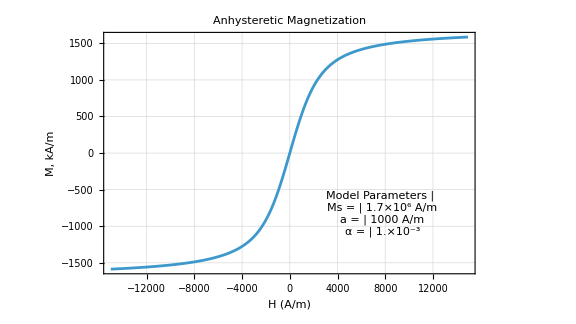

```mathematica
plotAnHystStressFig2 = ListLinePlot[
tblAnhys,
Frame->True,GridLines->Automatic,
FrameLabel->{"H (A/m)","M, kA/m"},
PlotLabel->"Anhysteretic Magnetization",
PlotRange->All,
AspectRatio->9/16,
Epilog->{Inset[paramBox,Scaled[{0.75,0.25}]]},
ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[] <>"Anhyst_Stress_Fig2.pdf",plotAnHystStressFig2];
```

```mathematica
Clear[{tblAnhys, plotAnHystStressFig2, dVertScale}]
```

#### Generate the plot with normalized magnetic field

Generate hysteresis table

```mathematica
tblAnhysNorm=Table[{h,fManOverMs[Quantity[h,"Amperes"/"Meters"]]},{h,-70000,70000,100.1}];
```

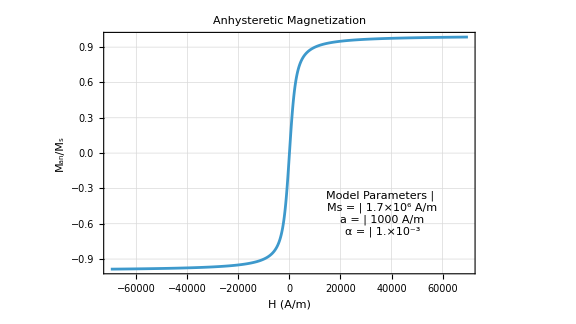

```mathematica
plotAnHystFig3Norm = ListLinePlot[
tblAnhysNorm,
Frame->True,GridLines->Automatic,
FrameLabel->{"H (A/m)","\!\(\*SubscriptBox[\(M\), \(an\)]\)/\!\(\*SubscriptBox[\(M\), \(s\)]\)"},
PlotLabel->"Anhysteretic Magnetization",
PlotRange->All,
AspectRatio->9/16,
Epilog->{Inset[paramBox,Scaled[{0.75,0.25}]]},
ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[] <>"Anhyst_Fig3_Norm.pdf",plotAnHystFig3Norm];
```

```mathematica
Clear[{tblAnhysNorm, plotAnHystFig3Norm}]
```

### Compare numerical and analytical derivatives

```mathematica
solAnHysMagnetoDMDH= eqnAnHysMagnetoDMDH/.subFig3;
solAnHysMagnetoDMDH=solAnHysMagnetoDMDH /.H -> Quantity[300, "Amperes"/"Meters"];
PrintUnitless[solAnHysMagnetoDMDH[[2]], Label->"dM_an/dH", Precision->19]
```

ReplaceAll::reps: {subFig3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

PrintUnitless[subFig3,Label→dM_an/dH,Precision→19]

```mathematica
(*Build the anhysteretic expression from your symbolic equation*)
exprDManDH=(eqnAnHysMagnetoDMDH/. subFig3)[[2]];

(*Define the anhysteretic magnetization M_an as a function of H*)
fDManDH[H_]:=Evaluate[(exprDManDH/. H->H)];
```

ReplaceAll::reps: {subFig3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
tblAnhysDmanDH=Table[{h,fDManDH[Quantity[h,"Amperes"/"Meters"]]},{h,-70000,70000,100.1}];
Take[tblAnhysDmanDH,{699,701}]//TableForm
```

-130.2 | subFig3
-30.1 | subFig3
70. | subFig3

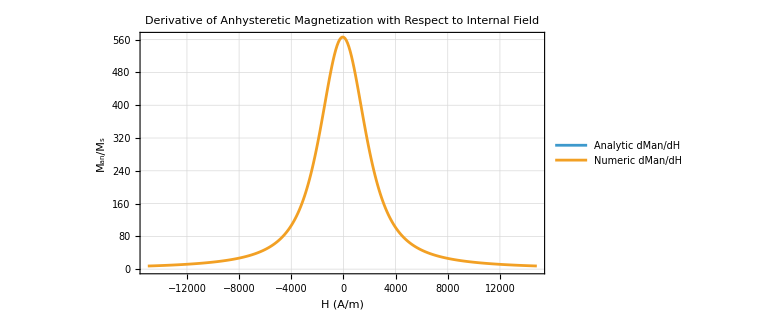

```mathematica
plotAnHystDmanDH = ListLinePlot[
{tblAnhysDmanDH, tblAnhysNumDer},
Frame->True,GridLines->Automatic,
FrameLabel->{"H (A/m)","\!\(\*SubscriptBox[\(M\), \(an\)]\)/\!\(\*SubscriptBox[\(M\), \(s\)]\)"},
PlotLabel->"Derivative of Anhysteretic Magnetization with Respect to Internal Field",
PlotRange->All,
AspectRatio->9/16,
ImageSize->Large,
PlotLegends->{"Analytic dMan/dH","Numeric dMan/dH"}
]
```

```mathematica
Export[NotebookDirectory[] <>"Anhyst_DmanDH.pdf",plotAnHystDmanDH];
```

```mathematica
Clear[{plotAnHystDmanDH, tblAnhysDmanDH}]
```

## Validation using Figure 9 in [2]

### Define the values

```mathematica
dMToMsInput = 0.2;
dMsInput = Quantity[1.6*10^6, "Amperes"/"Meters"]; PrintMagField[dMsInput,Label->"M_s", Precision->9]
dMInput = Quantity[0.00, "Amperes"/"Meters"]; PrintMagField[dMInput,Label->"M", Precision->9]
daInput = Quantity[1100, "Amperes"/"Meters"]; PrintMagField[daInput,Label->"a", Precision->9]
dkInput = Quantity[1000, "Amperes"/"Meters"]; PrintMagField[dkInput,Label->"k", Precision->9]
dαInput = 1.6*10^-3;PrintUnitless[dαInput, Label->"α", Precision->9]
dcInput = 0.2;PrintUnitless[dcInput, Label->"c", Precision->9]
dkInput = 400;PrintUnitless[dkInput, Label->"k", Precision->9]
dθInput = 0°; PrintAngle[dθInput, Label->"θ", Precision ->9]
dσ0Input = Quantity[00, "Megapascals"]; PrintPress[dσ0Input, Label->"θ_0", Precision->9]
μoInput = UnitConvert[Quantity["MagneticConstant"],"Henries"/"Meters"];  PrintPermeability[μoInput, Label->"μ_0", Precision->9]
```

M_s: 1.6×10^6 A/m (20106.193 Oe)

M: 0. A/m (0. Oe)

a: 1100. A/m (13.8230077 Oe)

k: 1000. A/m (12.5663706 Oe)

α: 0.001600000 (0.001600000)

c: 0.200000000 (0.200000000)

k: 400.000000000 (400.000000000)

θ: 0.000000000 ° (0.000000000 rad)

θ_0: 0. kPa (0. lbf/in^20. bar)

μ_0: 1.25663706×10^-6 H/m (3.19185814×10^-8 H/in)

### Define substitution rules

```mathematica
subFig9= {Ms->dMsInput, a->daInput, d->dkInput,
α->dαInput, c->dcInput,k->dkInput,
θ->dθInput, σ0->dσ0Input, μo->μoInput, M->dMInput};
subFig9 = Flatten[{subFig9,  γ1->(dγ1Input/.subFig9),  γ2->(dγ2Input/.subFig9)}]
```

{Ms→1.6×10^6 A/m,a→1100 A/m,d→400,α→0.0016,c→0.2,k→400,θ→0,σ0→0 MPa,μo→1.25663706×10^-6 H/m,M→0. A/m,γ1→4.×10^-18 m^2/A^2,γ2→2.×10^-30 m^4/A^4}

Calculate the anhysteretic value for this test point:

```mathematica
solAnHysMagnetoDMDH= eqnAnHysMagnetoDMDH/.subFig9;
solAnHysMagnetoDMDH=solAnHysMagnetoDMDH /.H -> Quantity[300, "Amperes"/"Meters"];
PrintUnitless[solAnHysMagnetoDMDH[[2]], Label->"dM_an/dH", Precision->19]
```

PrintUnitless[(Csch[(1/1100 m/A) (Hσ+300. A/m)]^2 (-1/1100 m/A)+(1100 A/m)/(Hσ+300. A/m)^2) (1.6×10^6 A/m),Label→dM_an/dH,Precision→19]

```mathematica
eqnJAIntegrated/.subFig9
```

0. A/m==0.833333 ((-3.52×10^8 A^2/m^2)/(H+Hσ+0. A/m)+H (Man+0. A/m) (-0.0016 Man+0. A/m+(3.14159265×10^-9 H/m)/δ)+Coth[(H+Hσ+0. A/m) (1/1100 m/A)] (320000. A/m))